正在演化 TCCT 宇宙... (目标: 2000 步)

正在生成物理分析与拟合报告 (含早期去噪)...

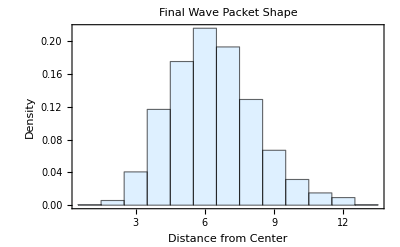
-Graphics- | -Graphics-
-Graphics- |

```mathematica
ClearAll["Global`*"];
SeedRandom[];

(* 1. 核心演化引擎 (Strict Engine) - 保持绝对不变 *)
rccRigidStep[g_Graph] := Module[{
   allEdges, activeEdges, candidates, selectedPair,
   e1, e2, x, y, z, w,
   newActive, inertEdges
   },
  
  allEdges = EdgeList[g];
  activeEdges = Cases[allEdges, _UndirectedEdge];
  
  If[Length[activeEdges] < 2, Return[g]];
  
  candidates = RandomSample[activeEdges, Min[Length[activeEdges], 120]];
  selectedPair = {};
  
  Do[
   e1 = candidates[[i]];
   Do[
    e2 = candidates[[j]];
    If[Length[Intersection[List @@ e1, List @@ e2]] == 1,
     selectedPair = {e1, e2};
     Goto["FoundPair"];
     ];
    , {j, i + 1, Length[candidates]}];
   , {i, 1, Length[candidates] - 1}];
  
  Return[g];
  
  Label["FoundPair"];
  {e1, e2} = selectedPair;
  y = Intersection[List @@ e1, List @@ e2][[1]];
  x = Complement[List @@ e1, {y}][[1]];
  z = Complement[List @@ e2, {y}][[1]];
  
  w = Max[VertexList[g]] + 1;
  
  newActive = {UndirectedEdge[x, z], UndirectedEdge[x, w], UndirectedEdge[w, z]};
  inertEdges = {DirectedEdge[x, y], DirectedEdge[y, z]};
  
  Graph[VertexList[g] ~Join~ {w}, 
   Union[Complement[allEdges, {e1, e2}], newActive, inertEdges]]
  ];

(* ========================================================== *)
(* 2. 演化实验 (提高采样频率) *)
(* ========================================================== *)

universe = CompleteGraph[6]; 
steps = 2000; (* 稍微增加步数让色散特征更明显 *)

fieldData = {}; 
nodeHistory = {}; 

Print[Style["正在演化 TCCT 宇宙... (目标: " <> ToString[steps] <> " 步)", Blue, Bold]];

Monitor[
  Do[
   universe = rccRigidStep[universe];
   
   (* 【修改】提高采样频率: 每 10 步测量一次，获取海量数据点 *)
   If[Mod[i, 10] == 0,
    activeEdges = Cases[EdgeList[universe], _UndirectedEdge];
    activeNodes = Union[Flatten[List @@@ activeEdges]];
    
    If[Length[activeNodes] > 0,
       dists = (GraphDistance[universe, 1, #] & /@ activeNodes);
       validDists = Select[dists, NumericQ]; 
       
       If[Length[validDists] > 1,
          currentRadius = Mean[validDists];
          currentWidth = StandardDeviation[validDists]; (* 新增：测量波包宽度 *)
          AppendTo[fieldData, {i, currentRadius, currentWidth}];
       ];
    ];
    AppendTo[nodeHistory, VertexCount[universe]];
   ];
   
   , {i, 1, steps}],
  Row[{ProgressIndicator[i, {0, steps}], " Step: ", i, " | Nodes: ", VertexCount[universe]}]
];

(* ========================================================== *)
(* 3. 物理分析与高精度拟合 (修正版) *)
(* ========================================================== *)
Print["\n正在生成物理分析与拟合报告 (含早期去噪)..."];

If[Length[fieldData] < 10,
   Print[Style["错误：数据点不足，请等待演化完成或降低采样间隔。", Red, Bold]],
   
   (* 数据拆分 *)
   radiusData = fieldData[[All, {1, 2}]];
   widthData = fieldData[[All, {1, 3}]];
   
   (* ============================================== *)
   (* 核心修改：切除前500步的“离散量子涨落”噪音 *)
   (* （如果你的总步数较少，可以把 500 改成 300） *)
   (* ============================================== *)
   cutoffStep = 600; 
   adultRadiusData = Select[radiusData, #[[1]] > cutoffStep &];
   
   (* 1. 光速拟合 (线性) - 仅使用成年期平稳数据 *)
   lmC = LinearModelFit[adultRadiusData, t, t];
   
   (* 提取真实的斜率(极限光速) 和 截距(大爆炸导致的相位延迟) *)
   c = lmC["BestFitParameters"][[2]];
   intercept = lmC["BestFitParameters"][[1]];
   r2C = lmC["RSquared"];

   (* 绘图：依然展示全图散点，但只画出真实的渐近线 *)
   plotC = ListPlot[radiusData, PlotStyle -> {Red, PointSize[0.01]}, 
     Frame -> True, FrameLabel -> {"Time (Steps)", "Mean Radius"},
     PlotLabel -> Style["Asymptotic Light Speed Limit (c)", 14, Bold],
     Epilog -> {
       (* 画出真正的极限光速拟合线（允许有截距） *)
       Blue, Dashed, Thickness[0.005], 
       Line[{{0, intercept}, {steps, intercept + c * steps}}],
       
       (* 画一条灰色的垂直虚线，标记“去噪阈值”在哪 *)
       Gray, Dotted, InfiniteLine[{{cutoffStep, 0}, {cutoffStep, 1}}],
       Text[Style["Quantum Noise Cutoff", Gray, 10, Background->White], {cutoffStep + 100, Max[radiusData[[All, 2]]]*0.2}],
       
       (* 显示高精度的 c 和 R^2 *)
       Text[Style["c = " <> ToString[NumberForm[c, {3, 4}]] <> 
                  "\n\!\(\*SuperscriptBox[\(R\), \(2\)]\) = " <> ToString[NumberForm[r2C, {4, 4}]], Blue, 12], 
            {steps*0.3, Max[radiusData[[All, 2]]]*0.8}]
     }
   ];

   (* 2. 波包色散拟合 (非线性 - 增加初始值估算) *)
   (* 自动估算初始值 w0 和 beta *)
   w0Guess = widthData[[1, 2]];
   betaGuess = (Last[widthData][[2]] - w0Guess)/steps;

   nlmW = Check[
     NonlinearModelFit[widthData, Sqrt[w0^2 + (beta*t)^2], {{w0, w0Guess}, {beta, betaGuess}}, t],
     $Failed
   ];

   If[nlmW =!= $Failed,
     w0Fit = w0 /. nlmW["BestFitParameters"];
     betaFit = beta /. nlmW["BestFitParameters"];
     r2W = nlmW["RSquared"];
     
     plotW = Show[
       ListPlot[widthData, PlotStyle -> {Orange, PointSize[0.01]}],
       Plot[nlmW[t], {t, 0, steps}, PlotStyle -> {Black, Dashed, Thickness[0.002]}],
       Frame -> True, FrameLabel -> {"Time (Steps)", "Wave Packet Width (σ)"},
       PlotLabel -> Style["Wave Dispersion Fit", 14, Bold],
       Epilog -> {Text[Style["β ~ " <> ToString[NumberForm[betaFit, {3, 4}]] <> "\n\!\(\*SuperscriptBox[\(R\), \(2\)]\) = " <> ToString[NumberForm[r2W, {4, 4}]], Black, 12], 
                  {steps*0.3, Max[widthData[[All, 2]]]*0.8}]}];
     ,
     plotW = Graphics[{Text[Style["Dispersion Fit Convergence Failed\n(Try increasing Steps)", Red, 12]]}, ImageSize -> 350];
   ];

   (* 3. 场强直方图 *)
   finalActiveEdges = Cases[EdgeList[universe], _UndirectedEdge];
   finalActiveNodes = Union[Flatten[List @@@ finalActiveEdges]];
   finalDists = Select[(GraphDistance[universe, 1, #] & /@ finalActiveNodes), NumericQ];

   plotShell = Histogram[finalDists, Automatic, "ProbabilityDensity",
     ChartStyle -> LightBlue, Frame -> True, 
     FrameLabel -> {"Distance from Center", "Density"},
     PlotLabel -> Style["Final Wave Packet Shape", 14, Bold]];

   (* 组合输出 *)
   Print[Grid[{{plotC, plotW}, {plotShell, SpanFromLeft}}, Spacings -> {2, 2}]]
]
```